```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,4,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,12,0.-1}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.7,0.0001,1,0]
```

2.

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

```mathematica
impu[ω_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ=RandomInteger[{1,14}]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
impu2[ω_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ=RandomInteger[{1,7}],μ1=RandomInteger[{8,14}]},(*μ1=RandomChoice[Delete[Range[1,14,1],μ],1][[1]];*)ReplacePart[κ,{{μ,μ},{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
tras[ω_,ϵ1_,a_,r_,c_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},lista={RandomSample[Join[Table[impu[ω,ϵ1],a],Table[impu2[ω,ϵ1],r],Table[impu[ω,0],c]]]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,75}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/75unitcells/resolve/test"<>ToString[x]<>".dat",Table[{ω,Mean[ParallelTable[tras[ω,0.5,x,0,75-x],2000]]},{ω,Range[0,3,0.01]}]],{x,Range[1,75,2]}]
```

```mathematica
y[a_,b_,c_]:=y[a,b,c]=Table[{ω,Mean[ParallelTable[tras[ω,0.5,99,a,b,c],2000]]},{ω,Range[0,3,0.01]}]
```

```mathematica
y[99,0,1]
```

{{0.,2.59691×10^-7},{0.2,2.69211×10^-6},{0.4,0.406571},{0.6,0.668959},{0.8,0.859428},{1.,0.92922},{1.2,0.438173},{1.4,0.505919},{1.6,0.410005},{1.8,1.21953},{2.,0.467771},{2.2,0.380284},{2.4,0.61214},{2.6,0.218236},{2.8,0.166406},{3.,1.01849×10^-7}}

```mathematica
432*300/60
```

```mathematica
2160/60
```

36

```mathematica
y[91,4,5]
```

{{0.,2.61215×10^-7},{0.2,2.69149×10^-6},{0.4,0.410452},{0.6,0.652222},{0.8,0.857798},{1.,0.93722},{1.2,0.425683},{1.4,0.493921},{1.6,0.407822},{1.8,1.19607},{2.,0.493751},{2.2,0.386708},{2.4,0.617288},{2.6,0.228219},{2.8,0.161236},{3.,1.01097×10^-7}}

```mathematica
y[81,9,10]
```

{{0.,2.57602×10^-7},{0.2,2.69115×10^-6},{0.4,0.408766},{0.6,0.656096},{0.8,0.83801},{1.,0.890037},{1.2,0.404124},{1.4,0.49394},{1.6,0.411285},{1.8,1.14585},{2.,0.501531},{2.2,0.404034},{2.4,0.603537},{2.6,0.237284},{2.8,0.147364},{3.,1.00674×10^-7}}

```mathematica
y[71,14,15]
```

{{0.,2.57719×10^-7},{0.2,2.69129×10^-6},{0.4,0.398055},{0.6,0.638283},{0.8,0.84236},{1.,0.866375},{1.2,0.414936},{1.4,0.515745},{1.6,0.409479},{1.8,1.10277},{2.,0.508109},{2.2,0.416871},{2.4,0.601663},{2.6,0.253292},{2.8,0.146464},{3.,1.00049×10^-7}}

```mathematica
y[61,20,19]
```

{{0.,2.58155×10^-7},{0.01,2.54423×10^-7},{0.02,2.67125×10^-7},{0.03,2.753×10^-7},{0.04,2.84393×10^-7},{0.05,2.94097×10^-7},{0.06,3.07138×10^-7},{0.07,3.21234×10^-7},{0.08,3.38335×10^-7},{0.09,3.56491×10^-7},{0.1,3.8164×10^-7},{0.11,4.14606×10^-7},{0.12,4.54964×10^-7},{0.13,5.05996×10^-7},{0.14,5.75115×10^-7},{0.15,6.65015×10^-7},{0.16,7.91877×10^-7},{0.17,9.77192×10^-7},{0.18,1.26424×10^-6},{0.19,1.74275×10^-6},{0.2,2.68577×10^-6},{0.21,4.9047×10^-6},{0.22,0.0000128854},{0.23,0.000118467},{0.24,0.0463314},{0.25,0.0556674},{0.26,0.0858819},{0.27,0.123286},{0.28,0.172538},{0.29,0.229587},{0.3,0.267787},{0.31,0.294496},{0.32,0.324249},{0.33,0.35791},{0.34,0.375293},{0.35,0.377904},{0.36,0.387612},{0.37,0.39082},{0.38,0.39933},{0.39,0.395835},{0.4,0.399253},{0.41,0.39629},{0.42,0.510973},{0.43,0.560168},{0.44,0.671796},{0.45,0.775836},{0.46,0.733372},{0.47,0.602025},{0.48,0.555533},{0.49,0.52698},{0.5,0.510044},{0.51,0.503716},{0.52,0.50096},{0.53,0.51132},{0.54,0.531784},{0.55,0.54393},{0.56,0.563866},{0.57,0.577007},{0.58,0.573733},{0.59,0.593629},{0.6,0.630474},{0.61,0.642702},{0.62,0.652903},{0.63,0.669197},{0.64,0.680371},{0.65,0.689432},{0.66,0.68845},{0.67,0.721059},{0.68,0.718873},{0.69,0.738388},{0.7,0.74636},{0.71,0.759161},{0.72,0.76067},{0.73,0.775345},{0.74,0.781511},{0.75,0.787497},{0.76,0.804753},{0.77,0.798977},{0.78,0.793063},{0.79,0.806799},{0.8,0.808189},{0.81,0.813995},{0.82,0.797132},{0.83,0.769087},{0.84,0.695143},{0.85,0.703016},{0.86,0.712958},{0.87,0.792986},{0.88,0.885733},{0.89,0.761348},{0.9,0.667333},{0.91,0.602675},{0.92,0.568587},{0.93,0.56017},{0.94,0.574054},{0.95,0.595363},{0.96,0.643457},{0.97,0.667886},{0.98,0.723067},{0.99,0.766733},{1.,0.793072},{1.01,0.87397},{1.02,0.840527},{1.03,0.679972},{1.04,0.44524},{1.05,0.349427},{1.06,0.358396},{1.07,0.360587},{1.08,0.354191},{1.09,0.346452},{1.1,0.335186},{1.11,0.337625},{1.12,0.33557},{1.13,0.329965},{1.14,0.329792},{1.15,0.323732},{1.16,0.343257},{1.17,0.339713},{1.18,0.354323},{1.19,0.375941},{1.2,0.39069},{1.21,0.409788},{1.22,0.418941},{1.23,0.438443},{1.24,0.422758},{1.25,0.442388},{1.26,0.459447},{1.27,0.448382},{1.28,0.475511},{1.29,0.466772},{1.3,0.473219},{1.31,0.482329},{1.32,0.484681},{1.33,0.484023},{1.34,0.494374},{1.35,0.493523},{1.36,0.490374},{1.37,0.505018},{1.38,0.495583},{1.39,0.492838},{1.4,0.502907},{1.41,0.492973},{1.42,0.496135},{1.43,0.49941},{1.44,0.494596},{1.45,0.477807},{1.46,0.478639},{1.47,0.470136},{1.48,0.458359},{1.49,0.460012},{1.5,0.443025},{1.51,0.4592},{1.52,0.431082},{1.53,0.440296},{1.54,0.443787},{1.55,0.430482},{1.56,0.431537},{1.57,0.418568},{1.58,0.410045},{1.59,0.413588},{1.6,0.408275},{1.61,0.416352},{1.62,0.403871},{1.63,0.41154},{1.64,0.398618},{1.65,0.40584},{1.66,0.434949},{1.67,0.452529},{1.68,0.479094},{1.69,0.522211},{1.7,0.573257},{1.71,0.647575},{1.72,0.737213},{1.73,0.886868},{1.74,1.11909},{1.75,1.4784},{1.76,1.8946},{1.77,1.52923},{1.78,1.38951},{1.79,1.26579},{1.8,1.11217},{1.81,0.932309},{1.82,0.726962},{1.83,0.553695},{1.84,0.43802},{1.85,0.369492},{1.86,0.362382},{1.87,0.370545},{1.88,0.392031},{1.89,0.42076},{1.9,0.44834},{1.91,0.461637},{1.92,0.486535},{1.93,0.498935},{1.94,0.50649},{1.95,0.510538},{1.96,0.519686},{1.97,0.524113},{1.98,0.515676},{1.99,0.525363},{2.,0.508369},{2.01,0.518407},{2.02,0.524432},{2.03,0.5131},{2.04,0.502019},{2.05,0.496406},{2.06,0.508165},{2.07,0.50101},{2.08,0.502482},{2.09,0.489887},{2.1,0.492973},{2.11,0.474562},{2.12,0.474183},{2.13,0.473424},{2.14,0.460532},{2.15,0.460508},{2.16,0.458845},{2.17,0.446483},{2.18,0.4225},{2.19,0.434431},{2.2,0.414191},{2.21,0.407217},{2.22,0.395226},{2.23,0.382197},{2.24,0.367504},{2.25,0.364491},{2.26,0.352758},{2.27,0.34475},{2.28,0.328574},{2.29,0.318148},{2.3,0.321044},{2.31,0.295527},{2.32,0.306886},{2.33,0.296702},{2.34,0.29029},{2.35,0.292455},{2.36,0.3055},{2.37,0.315009},{2.38,0.354753},{2.39,0.438986},{2.4,0.590545},{2.41,0.869246},{2.42,0.647871},{2.43,0.610521},{2.44,0.58062},{2.45,0.489971},{2.46,0.410769},{2.47,0.335679},{2.48,0.259538},{2.49,0.212393},{2.5,0.190478},{2.51,0.214176},{2.52,0.210017},{2.53,0.249336},{2.54,0.238701},{2.55,0.238666},{2.56,0.262126},{2.57,0.256282},{2.58,0.256398},{2.59,0.250485},{2.6,0.253389},{2.61,0.262589},{2.62,0.249488},{2.63,0.255139},{2.64,0.244865},{2.65,0.241951},{2.66,0.24019},{2.67,0.228592},{2.68,0.232109},{2.69,0.227547},{2.7,0.208525},{2.71,0.207416},{2.72,0.204261},{2.73,0.195187},{2.74,0.187644},{2.75,0.172535},{2.76,0.171796},{2.77,0.160958},{2.78,0.145884},{2.79,0.134484},{2.8,0.142146},{2.81,0.129552},{2.82,0.13073},{2.83,0.126206},{2.84,0.145892},{2.85,0.000430785},{2.86,0.0000162219},{2.87,4.92412×10^-6},{2.88,2.33967×10^-6},{2.89,1.35248×10^-6},{2.9,8.73663×10^-7},{2.91,6.10202×10^-7},{2.92,4.48227×10^-7},{2.93,3.46086×10^-7},{2.94,2.75402×10^-7},{2.95,2.24018×10^-7},{2.96,1.8492×10^-7},{2.97,1.56513×10^-7},{2.98,1.31882×10^-7},{2.99,1.13411×10^-7},{3.,9.95603×10^-8}}

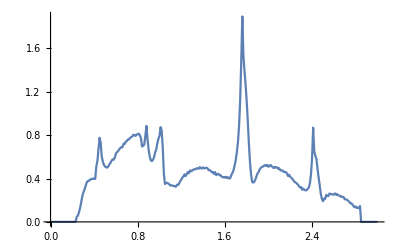

```mathematica
ListPlot[%94,Joined->True,PlotRange->All]
```

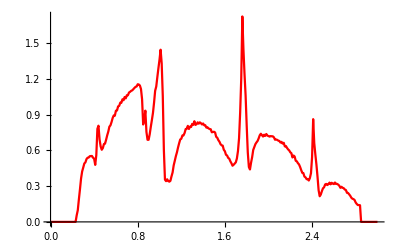

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test61.dat"],PlotStyle->Red,PlotRange->All]
```

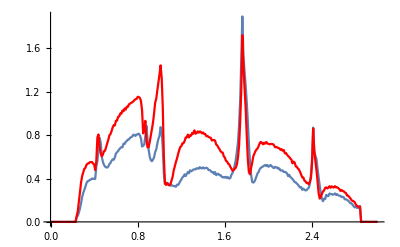

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test61.dat"],PlotStyle->Red,PlotRange->All],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test63.dat"],PlotStyle->Red,PlotRange->All],PlotRange->All]
```

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[21+2*x]<>".dat",y[21,x,79-x]],{x,Range[75,79,1]}]
```

$Aborted

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[11+2*x]<>".dat",y[11,x,89-x]],{x,Range[80,89,1]}]
```

```mathematica
y[51,24,25]
```

{{0.,2.59086×10^-7},{0.2,2.68368×10^-6},{0.4,0.402512},{0.6,0.628749},{0.8,0.825827},{1.,0.797355},{1.2,0.39149},{1.4,0.495817},{1.6,0.415114},{1.8,1.08835},{2.,0.536462},{2.2,0.430896},{2.4,0.576337},{2.6,0.268481},{2.8,0.127466},{3.,9.84206×10^-8}}

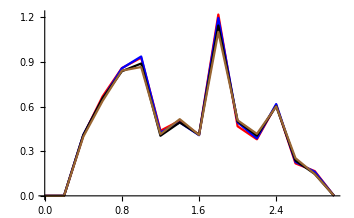

```mathematica
Show[ListLinePlot[%86,PlotStyle->Red],ListLinePlot[%87,PlotStyle->Blue],ListLinePlot[%88,PlotStyle->Black],ListLinePlot[%89,PlotStyle->Brown]]
```

```mathematica
Mean[ParallelTable[tras[1.5,0.5,99],10000]]
```

0.471418

```mathematica
Mean[ParallelTable[tras[1.5,0.5,99],10000]]
```

0.463648

```mathematica
Mean[ParallelTable[tras[1.5,0.5,99],10000]]
```

0.456185

```mathematica
Mean[ParallelTable[tras[1.5,0.5,99],10000]]
```

0.455095

```mathematica
Mean[ParallelTable[tras[1,0.5,99],10000]]
```

0.946412

```mathematica
Mean[ParallelTable[tras[1,0.5,99],10000]]
```

0.856637

```mathematica
Mean[ParallelTable[tras[1,0.5,99],10000]]
```

0.940444

```mathematica
Mean[ParallelTable[tras[1,0.5,10],10000]]
```

1.2305

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/30unitcells/resolve/test"<>ToString[51+2*x]<>".dat",Table[{ω,Mean[ParallelTable[tras[ω,0.5,x],2000]]},{ω,Range[0,3,0.01]}]],{x,Range[25,48,1]}]
```

```mathematica
Do[Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[41+2*x]<>".dat",Table[{ω,Mean[ParallelTable[tras[ω,0.5,x],2000]]},{ω,Range[0,3,0.01]}]],{x,Range[45,59,1]}]
```

```mathematica
Clear[impu,impu2]
```

```mathematica
RandomSample[Join[Table[impu[ω,ϵ1],51],Table[impu2[ω,ϵ1],25],Table[impu[ω,0],49-25]]]
```

```mathematica
{impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,0],impu[ω,0],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,0],impu[ω,0],impu[ω,0],impu[ω,0],impu2[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,0],impu[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,0],impu[ω,0],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,0],impu[ω,0],impu2[ω,ϵ1],impu[ω,0],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,0],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,0],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,0],impu[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,0],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,ϵ1],impu[ω,0],impu[ω,0],impu[ω,0],impu[ω,ϵ1],impu2[ω,ϵ1],impu[ω,0],impu2[ω,ϵ1],impu2,ϵ1],impu2[ω,ϵ1],impu[ω,ϵ1],impu2[ω,ϵ1],impu2[ω,ϵ1],impu[ω,0]}
```

```mathematica
Dimensions[%174]
```

{100}

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test99.dat",Table[{ω,Mean[ParallelTable[tras[ω,0.5,99],2000]]},{ω,Range[0,3,0.01]}]]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test99.dat

```mathematica
RandomSample[Join[Table[Tr[Inverse[impu[0,1]]],99],Table[Tr[Inverse[impu2[0,1]]],0],Table[Tr[Inverse[impu[0,0]]],1]]]
```

{-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,0.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ,-1.+0.0014 ⅈ}

```mathematica
Total[RandomSample[Join[Table[Tr[Inverse[impu[0,1]]],71],Table[Tr[Inverse[impu2[0,1]]],14],Table[Tr[Inverse[impu[0,0]]],15]]]]
```

-99.+0.14 ⅈ

```mathematica
1.1*4500
```

```mathematica
4950./60
```

82.5